```mathematica
enenrgyData=Import[FileNameJoin[{NotebookDirectory[],"data","energyData.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
PhiData=Import[FileNameJoin[{NotebookDirectory[],"data","Phi_0_10080.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
IsingEnergyData=Import[FileNameJoin[{NotebookDirectory[],"data","isingEnergy_0_10080.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

```mathematica
PhiData=Table[Import[FileNameJoin[{NotebookDirectory[],"data","all_phi","Phi_"<>name<>".csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ,{name,{"0_1000","1000_2000","2000_3000","3000_4000","4000_5000","5000_6000","6000_7000","7000_8000","8000_9000","9000_10080"}}];
PhiData=Join@@PhiData;

IsingEnergyData=Import[FileNameJoin[{NotebookDirectory[],"data","isingEnergy_0_10080.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

```mathematica
Length[PhiData]
```

10080

```mathematica
Length[IsingEnergyData]
```

10080

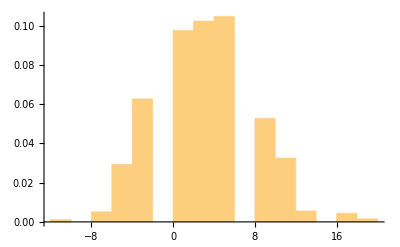

```mathematica
eH=Histogram[Mean/@IsingEnergyData,Automatic,"PDF"]
```

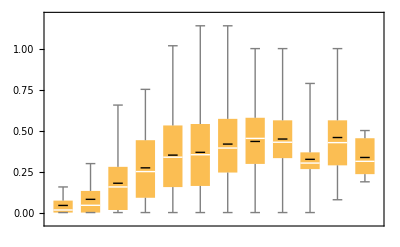

```mathematica
BoxWhiskerChart[#ᵀ⟦2⟧&/@SortBy[GatherBy[{Mean/@IsingEnergyData⟦1;;Length[PhiData]⟧,Min/@(Select[#,NumberQ]&/@PhiData)}ᵀ,First],#⟦1,1⟧&],"Mean"]
```

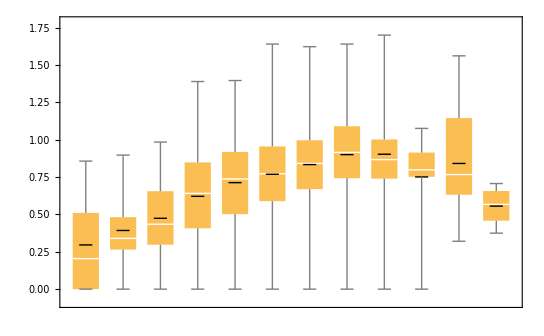

```mathematica
BoxWhiskerChart[#ᵀ⟦2⟧&/@SortBy[GatherBy[{Mean/@IsingEnergyData⟦1;;Length[PhiData]⟧,Mean/@(Select[#,NumberQ]&/@PhiData)}ᵀ,First],#⟦1,1⟧&],"Mean"]
```

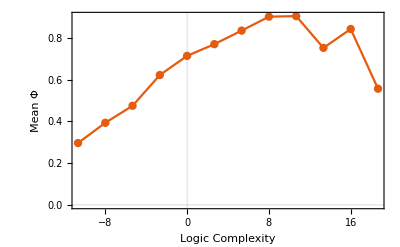

```mathematica
ListPlot[Sort[Mean/@GatherBy[{Mean/@IsingEnergyData⟦1;;Length[PhiData]⟧,Mean/@(Select[#,NumberQ]&/@PhiData)}ᵀ,First]],PlotTheme->"Scientific",FrameLabel->{"Logic Complexity","Mean Φ"},Joined->True,Mesh->Full]
```

```mathematica
Length/@SortBy[GatherBy[{Mean/@IsingEnergyData⟦1;;Length[PhiData]⟧,Mean/@(Select[#,NumberQ]&/@PhiData)}ᵀ,First],First]
```

{24,104,592,1264,1968,2064,2112,1064,656,112,88,32}

```mathematica
ListPlot[Sort[Mean/@GatherBy[{Mean/@IsingEnergyData⟦1;;Length[PhiData]⟧,Mean/@(Select[#,NumberQ]&/@PhiData)}ᵀ,First]],PlotTheme->"Scientific",FrameLabel->{"Logic Complexity","Mean Φ"},Joined->True,Mesh->Full]
```

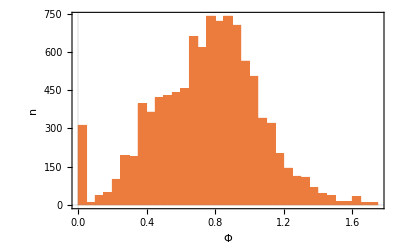

```mathematica
Histogram[Mean/@PhiData,PlotTheme->"Scientific",FrameLabel->{"Φ",n}]
```

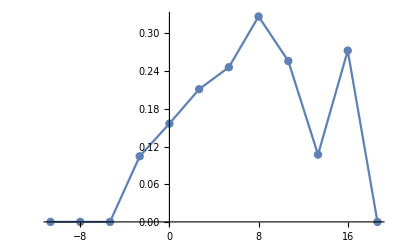

```mathematica
rPhi=ListPlot[Sort[{#⟦1,1⟧,Count[#,{x1_,x2_}/;x2>1.0]/Length[#]}&/@Reverse@Sort[GatherBy[{Mean/@IsingEnergyData⟦1;;Length[PhiData]⟧,Mean/@(Select[#,NumberQ]&/@PhiData)}ᵀ,First]]],Joined->True,Mesh->Full]
```

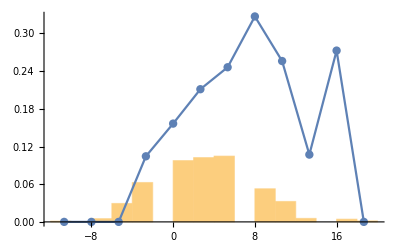

```mathematica
Show[eH,rPhi]
```

```mathematica
Count[{{1,2},{3,4},{5,6}},{x1_,x2_}/;x2>3]
```

2

```mathematica
DateObject[{2018,12,7}]-DateObject[{2018,8,5}]
```

124 days